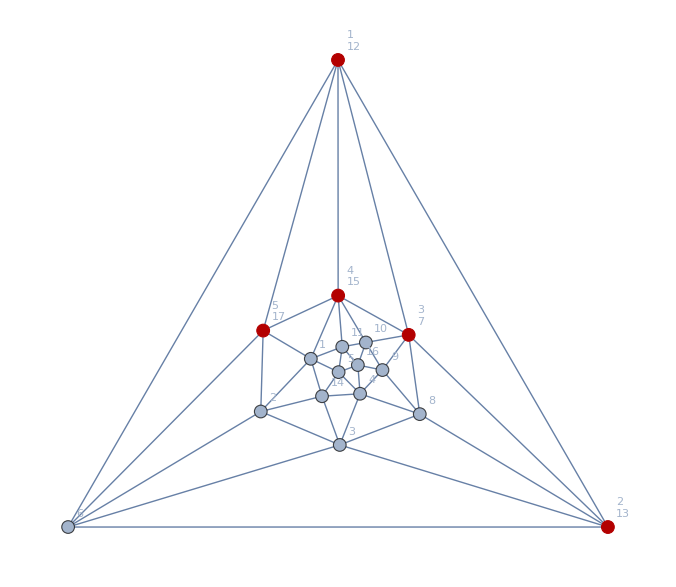

```mathematica
Graph[plantri8,GraphHighlight->{12,13,7,15,17},VertexLabels->{12->Column[{1,12},Alignment->Center],
13->Column[{2,13},Alignment->Center],
7->Column[{3,7},Alignment->Center],
15->Column[{4,15},Alignment->Center],
17->Column[{5,17},Alignment->Center]}]
```

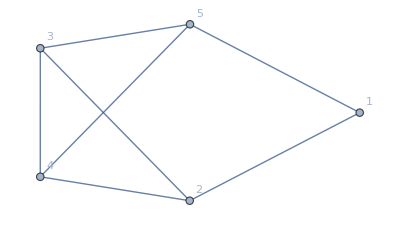

```mathematica
Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,5],UndirectedEdge[5,1],UndirectedEdge[2,4],UndirectedEdge[3,5]},VertexLabels->"Name"]
```

```mathematica
ChromaticPolynomial[plantri8,4]
```

528

```mathematica
ChromaticPolynomial[VertexContract[plantri8,{13,17}],4]
```

168

```mathematica
VertexContract[plantri8,{13,17}]
```

```mathematica
ChromaticPolynomial[EdgeDelete[VertexContract[plantri8,{13,17}],UndirectedEdge[12,7]],4]
```

504

```mathematica
ChromaticPolynomial[VertexContract[plantri8,{12,7}],4]
```

816

```mathematica
ChromaticPolynomial[EdgeDelete[plantri8,UndirectedEdge[12,7]],4]
```

1344

```mathematica
528+816
```

1344

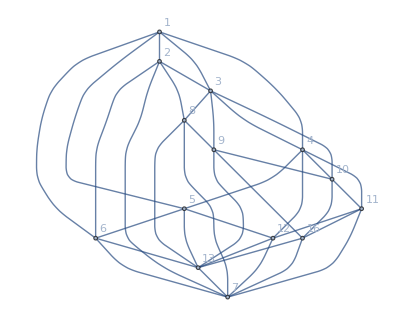

```mathematica
Graph[EmbedGraphInPlantri8[allGraphs5,29608],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],4],{k,allGraphs5AtomKeys}]
```

{-Graphics-295240→0,-Graphics-295250→240,-Graphics-295270→144,-Graphics-295330→480,-Graphics-295371→336,-Graphics-295510→264,-Graphics-295600→744,-Graphics-296050→144,-Graphics-296080→0,-Graphics-296330→240,-Graphics-297670→240,-Graphics-297681→336,-Graphics-297970→240,-Graphics-298571→336,-Graphics-298881→264,-Graphics-302530→264,-Graphics-302621→696,-Graphics-303340→192,-Graphics-304961→384,-Graphics-305861→264,-Graphics-317110→216,-Graphics-317140→72,-Graphics-317380→192,-Graphics-319540→192,-Graphics-319840→96,-Graphics-324411→480,-Graphics-326841→288,-Graphics-360850→216,-Graphics-360860→192,-Graphics-361120→192,-Graphics-361660→72,-Graphics-361940→96,-Graphics-368170→312,-Graphics-368980→120,-Graphics-382810→168,-Graphics-383080→216,-Graphics-390141→384,-Graphics-492070→264,-Graphics-492081→384,-Graphics-492100→192,-Graphics-492161→696,-Graphics-492201→264,-Graphics-499631→504,-Graphics-499721→624,-Graphics-514750→312,-Graphics-514780→120,-Graphics-522321→432,-Graphics-560111→480,-Graphics-560121→288,-Graphics-567701→432,-Graphics-582881→384,-Graphics-590481→384}